```mathematica
gassmann = With[{Pmod = Kd+(1-Kd/Km)^2/(phi/Kf-Kd/Km^2+(1-phi)/Km)+4/3*μ},
SymmetrizedArray[{
Sequence@@Thread[{{1,1}, {2,2}, {3,3}}-> Pmod],
Sequence@@Thread[{{4,4}, {5,5}, {6,6}}-> μ],
Sequence@@Thread[{{1,2}, {1,3}, {2,3}}-> Pmod-2μ],
Sequence@@Thread[{{2,1}, {3,1}, {3,2}}-> Pmod-2μ]
}]
];
squirt = With[{
lamb=(16*(15*l*(-Kf+l)+4*(-3*Kf+5*l)*m+4*m**2))/(45.0*(l+m)*(3*Kf+4*m)),
mu=(16*m)/(45.0*(l+m))},
SymmetrizedArray[{
Sequence@@Thread[{{1,1}, {2,2}, {3,3}}-> lamb+2mu],
Sequence@@Thread[{{4,4}, {5,5}, {6,6}}-> μ],
Sequence@@Thread[{{1,2}, {1,3}, {2,3}}-> Pmod-2μ],
Sequence@@Thread[{{2,1}, {3,1}, {3,2}}-> Pmod-2μ]
}]
];
```

Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)+(4 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | 0 | 0 | 0
Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)+(4 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | 0 | 0 | 0
Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)-(2 μ)/3 | Kd+(1-Kd/Km)^2/(-Kd/Km^2+(1-phi)/Km+phi/Kf)+(4 μ)/3 | 0 | 0 | 0
0 | 0 | 0 | μ | 0 | 0
0 | 0 | 0 | 0 | μ | 0
0 | 0 | 0 | 0 | 0 | μ

```mathematica
epsilon*(l+2*m)*
```

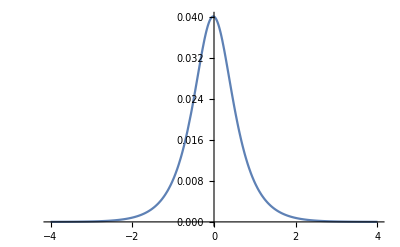

```mathematica
Plot[10^omega/(1+10^(2 omega))/(12+ 10^(2 omega)/(1+10^(2 omega))), {omega, -4, 4}]
```

```mathematica
10^omega/(1+10^(2 omega))//FortranForm
```

10**omega/(1 + 10**(2*omega))

```mathematica
(10^omega A)/(1+10^(2 omega))/((10^(2 omega) A)/(1+10^(2 omega))+f)/.omega->0//FullSimplify
```

A/(A+2 f)

```mathematica
Solve[maxQ ==A/(A+2 f), A]
```

```mathematica
{{A->ef}}
```

```mathematica
ComplexExpand[f + A(ⅈ*(10^omega))/(1+ⅈ*(10^omega))]
```

(ⅈ 10^omega A)/(1+10^(2 omega))+(10^(2 omega) A)/(1+10^(2 omega))+f

```mathematica
Thread[{{1,1}, {2,2}, {3,3}}-> Pmod]
```

{{1,1}→Pmod,{2,2}→Pmod,{3,3}→Pmod}

```mathematica
?Symmetric
```

```mathematica
ThermodynamicData["Water", "DynamicViscosity", {"Temperature"->Quantity[100, "DegreesCelsius"], "Pressure"-> Quantity[100, "Megapascals"]}]
```

1733.51 m/s

```mathematica
ThermodynamicData["Water", "IsothermalBulkModulus", {"Temperature"->Quantity[100, "DegreesCelsius"], "Pressure"-> Quantity[100, "Megapascals"]}]
```

2.70513×10^9 Pa

```mathematica
ThermodynamicData[ "Water","Density",{"Temperature"->{Quantity[100, "DegreesCelsius"],Quantity[1700, "DegreesCelsius"]}, "Pressure"-> Quantity[100, "Megapascals"]}]
```

{999.762 kg/m^3,105.117 kg/m^3}

```mathematica
|
```

```mathematica
temp = Import["~/Downloads/temperature_depth_profile.csv"]//Rest
```

{{-5,273.282},{-4,331.225},{-3,389.169},{-2,447.113},{-1,505.056},{0,563.},{1,620.944},{2,678.887},{3,736.831},{4,794.775},{5,852.718},{6,910.662},{7,968.606},{8,1026.55},{9,1084.49},{10,1142.44},{11,1200.38},{12,1258.32},{13,1316.27},{14,1374.21},{15,1432.15},{16,1490.1},{17,1548.04},{18,1605.99},{19,1663.93},{20,1721.87},{21,1779.82},{22,1837.76},{23,1895.7},{24,1953.65},{25,2011.59}}

```mathematica
10 (6+#)&/@Range[-6,20,1]
```

{0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260}

```mathematica
conditions = {#1, Quantity[10 (6+#1),"Megapascals"],Quantity[#2, "Kelvins"]}&@@@temp;
```

```mathematica
conditions
```

{{-5,10 MPa,273.282 K},{-4,20 MPa,331.225 K},{-3,30 MPa,389.169 K},{-2,40 MPa,447.113 K},{-1,50 MPa,505.056 K},{0,60 MPa,563. K},{1,70 MPa,620.944 K},{2,80 MPa,678.887 K},{3,90 MPa,736.831 K},{4,100 MPa,794.775 K},{5,110 MPa,852.718 K},{6,120 MPa,910.662 K},{7,130 MPa,968.606 K},{8,140 MPa,1026.55 K},{9,150 MPa,1084.49 K},{10,160 MPa,1142.44 K},{11,170 MPa,1200.38 K},{12,180 MPa,1258.32 K},{13,190 MPa,1316.27 K},{14,200 MPa,1374.21 K},{15,210 MPa,1432.15 K},{16,220 MPa,1490.1 K},{17,230 MPa,1548.04 K},{18,240 MPa,1605.99 K},{19,250 MPa,1663.93 K},{20,260 MPa,1721.87 K},{21,270 MPa,1779.82 K},{22,280 MPa,1837.76 K},{23,290 MPa,1895.7 K},{24,300 MPa,1953.65 K},{25,310 MPa,2011.59 K}}

```mathematica
Prepend[Range[-5,25]]
```

Prepend[{-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}]

```mathematica
(Flatten[Table[ThermodynamicData[ fluid,property,{ "Pressure"->#2,"Temperature"->#3}&@@@conditions]//QuantityMagnitude,{fluid, {"CarbonDioxide", "Water"}},{property,{ "IsothermalBulkModulus", "Density",  "DynamicViscosity"}}],1]~Prepend~Range[-5,25]//Transpose)
```

{{-5,1.69457×10^8,973.393,0.00011369,2.02307×10^9,1004.83,0.00176265},{-4,4.84519×10^7,735.724,0.0000616276,2.37542×10^9,992.678,0.00048467},{-3,4.42237×10^7,599.642,0.0000481466,2.12718×10^9,960.355,0.000248349},{-2,5.70208×10^7,549.297,0.0000460135,1.68791×10^9,916.476,0.000165316},{-1,7.24452×10^7,526.559,0.0000465143,1.23008×10^9,863.286,0.000126567},{0,8.86274×10^7,514.4,0.0000478496,8.31048×10^8,801.058,0.000104482},{1,1.05087×10^8,507.222,0.0000495013,5.24963×10^8,729.477,0.0000895321},{2,1.21649×10^8,502.736,0.0000512755,3.19719×10^8,649.343,0.0000780326},{3,1.38237×10^8,499.848,0.0000530868,2.04395×10^8,565.922,0.0000689535},{4,1.54812×10^8,497.972,0.0000548945,1.54693×10^8,491.043,0.0000625716},{5,1.71355×10^8,496.771,0.0000566784,1.40089×10^8,434.116,0.0000589069},{6,1.87856×10^8,496.037,0.0000584282,1.40964×10^8,394.376,0.0000572133},{7,2.0431×10^8,495.634,0.0000601394,1.48663×10^8,366.962,0.0000567176},{8,2.20714×10^8,495.472,0.0000618105,1.5946×10^8,347.633,0.000056914},{9,2.37067×10^8,495.488,0.0000634416,1.71733×10^8,333.58,0.0000575131},{10,2.5337×10^8,495.638,0.0000650341,1.84741×10^8,323.057,0.0000583523},{11,2.69624×10^8,495.888,0.0000665895,1.98124×10^8,314.973,0.0000593384},{12,2.85828×10^8,496.216,0.00006811,2.117×10^8,308.627,0.0000604154},{13,3.01986×10^8,496.602,0.0000695976,2.2537×10^8,303.558,0.0000615491},{14,3.18098×10^8,497.034,0.0000710545,2.39081×10^8,299.448,0.0000627172},{15,3.34166×10^8,497.499,0.0000724829,2.528×10^8,296.074,0.0000639054},{16,3.50191×10^8,497.991,0.0000738847,2.66511×10^8,293.278,0.0000651038},{17,3.66175×10^8,498.501,0.0000752619,2.80204×10^8,290.94,0.0000663057},{18,3.8212×10^8,499.026,0.0000766165,2.93871×10^8,288.971,0.0000675064},{19,3.98026×10^8,499.561,0.0000779501,3.0751×10^8,287.305,0.0000687025},{20,4.13895×10^8,500.102,0.0000792644,3.21119×10^8,285.888,0.0000698917},{21,4.29729×10^8,500.648,0.0000805609,3.34697×10^8,284.678,0.0000710723},{22,4.45528×10^8,501.195,0.0000818412,3.48245×10^8,283.642,0.0000722431},{23,4.61294×10^8,501.742,0.0000831065,3.61762×10^8,282.755,0.0000734033},{24,4.77027×10^8,502.288,0.0000843582,3.7525×10^8,281.993,0.0000745523},{25,4.9273×10^8,502.832,0.0000855974,3.88708×10^8,281.338,0.0000756897}}